```mathematica
L[x_]= (γ*x'[t] + k*x[t] - F0*(1 - Exp[-t/τ]))^2
```

(-((1-ⅇ^(-t/τ)) F0)+k x[t]+γ x'[t])^2

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[L[x],{x[t]},{t}]//FullSimplify
```

{k (F0-k x[t])+γ^2 x''[t]==(ⅇ^(-t/τ) F0 (γ+k τ))/τ}

```mathematica
DSolve[{k (F0-k x[t])+γ^2 x''[t]==(ⅇ^(-t/τ) F0 (γ+k τ))/τ,x[t1]==xt1,x[0]==x0},{x[t]},{t}]//FullSimplify
```

{{x[t]→1/(2 k (-γ+k τ))ⅇ^(-(k t)/γ-(t+t1)/τ) (ⅇ^((k t1)/γ+t/τ) (-1+ⅇ^((2 k t)/γ)) F0 k τ+ⅇ^(t1/τ) (ⅇ^((k t)/γ) F0 k τ-ⅇ^((k (t+2 t1))/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) F0 (γ-k τ)-ⅇ^((k (t+2 t1))/γ+t/τ) F0 (γ-k τ)+ⅇ^((k (2 t+t1))/γ+t/τ) (F0-k xt1) (γ-k τ)+ⅇ^((k t1)/γ+t/τ) (-F0+k xt1) (γ-k τ)-ⅇ^(t ((2 k)/γ+1/τ)) (F0 γ+k x0 (-γ+k τ))+ⅇ^((2 k t1)/γ+t/τ) (F0 γ+k x0 (-γ+k τ)))) (-1+Coth[(k t1)/γ])}}

```mathematica
x1[t_]=1/(2 k (-γ+k τ))ⅇ^(-(k t)/γ-(t+t1)/τ) (ⅇ^((k t1)/γ+t/τ) (-1+ⅇ^((2 k t)/γ)) F0 k τ+ⅇ^(t1/τ) (ⅇ^((k t)/γ) F0 k τ-ⅇ^((k (t+2 t1))/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) F0 (γ-k τ)-ⅇ^((k (t+2 t1))/γ+t/τ) F0 (γ-k τ)+ⅇ^((k (2 t+t1))/γ+t/τ) (F0-k xt1) (γ-k τ)+ⅇ^((k t1)/γ+t/τ) (-F0+k xt1) (γ-k τ)-ⅇ^(t ((2 k)/γ+1/τ)) (F0 γ+k x0 (-γ+k τ))+ⅇ^((2 k t1)/γ+t/τ) (F0 γ+k x0 (-γ+k τ)))) (-1+Coth[(k t1)/γ])
```

1/(2 k (-γ+k τ))ⅇ^(-(k t)/γ-(t+t1)/τ) (ⅇ^((k t1)/γ+t/τ) (-1+ⅇ^((2 k t)/γ)) F0 k τ+ⅇ^(t1/τ) (ⅇ^((k t)/γ) F0 k τ-ⅇ^((k (t+2 t1))/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) F0 (γ-k τ)-ⅇ^((k (t+2 t1))/γ+t/τ) F0 (γ-k τ)+ⅇ^((k (2 t+t1))/γ+t/τ) (F0-k xt1) (γ-k τ)+ⅇ^((k t1)/γ+t/τ) (-F0+k xt1) (γ-k τ)-ⅇ^(t ((2 k)/γ+1/τ)) (F0 γ+k x0 (-γ+k τ))+ⅇ^((2 k t1)/γ+t/τ) (F0 γ+k x0 (-γ+k τ)))) (-1+Coth[(k t1)/γ])

```mathematica
Lextremized = L[x1]//FullSimplify
```

(4 ⅇ^((2 k t)/γ-(2 t1)/τ) (-ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (-F0+k xt1) (γ-k τ)+ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2)/((-1+ⅇ^((2 k t1)/γ))^2 (γ-k τ)^2)

```mathematica
Integrate[Lextremized,{t,0,t1}]
```

(ⅇ^(-(2 t1)/τ) γ (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(k (γ-k τ)^2)

```mathematica
A[xt1_,x0_]=(ⅇ^(-(2 t1)/τ) γ (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(k (γ-k τ)^2)
```

(ⅇ^(-(2 t1)/τ) γ (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(k (γ-k τ)^2)

```mathematica
P[xt1_,x0_]= Exp[-A[xt1,x0]/(4*γ*T)]/((2 √π)/(√((k (1+Coth[(k t1)/γ]))/T)))
```

```mathematica
(ⅇ^(-(ⅇ^(-(2 t1)/τ) (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(4 k T (γ-k τ)^2)) √((k (1+Coth[(k t1)/γ]))/T))/(2 √π)//FullSimplify
```

(ⅇ^(-(ⅇ^(-(2 t1)/τ) (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(4 k T (γ-k τ)^2)) √((k (1+Coth[(k t1)/γ]))/T))/(2 √π)

```mathematica
ⅇ^(-(ⅇ^(-(2 t1)/τ) (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(4 k T (γ-k τ)^2))
```

```mathematica
Collect[-(ⅇ^(-(2 t1)/τ) (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(4 k T (γ-k τ)^2),xt1]
```

-(ⅇ^(2 t1 (k/γ+1/τ)-(2 t1)/τ) k xt1^2 (-1+Coth[(k t1)/γ]))/(4 T)-1/(4 k T (γ-k τ)^2)ⅇ^(-(2 t1)/τ) xt1 (-2 ⅇ^((k t1)/γ+t1 (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t1 (k/γ+1/τ)) F0 k (γ-k τ)^2+2 ⅇ^(t1 (k/γ+1/τ)+t1/τ) k (γ-k τ) (F0 γ+k x0 (-γ+k τ))) (-1+Coth[(k t1)/γ])-1/(4 k T (γ-k τ)^2)ⅇ^(-(2 t1)/τ) (ⅇ^((2 k t1)/γ) F0^2 k^2 τ^2+2 ⅇ^((k t1)/γ+t1 (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t1 (k/γ+1/τ)) F0^2 (γ-k τ)^2-2 ⅇ^((k t1)/γ+t1/τ) F0 k τ (F0 γ+k x0 (-γ+k τ))-2 ⅇ^(t1 (k/γ+1/τ)+t1/τ) F0 (γ-k τ) (F0 γ+k x0 (-γ+k τ))+ⅇ^((2 t1)/τ) (F0 γ+k x0 (-γ+k τ))^2) (-1+Coth[(k t1)/γ])

```mathematica
(ⅇ^(-b^2/(4 a)+c) √π)/(√-a)/.{a->-(ⅇ^(2 t1 (k/γ+1/τ)-(2 t1)/τ) k  (-1+Coth[(k t1)/γ]))/(4 T),b->-1/(4 k T (γ-k τ)^2)ⅇ^(-(2 t1)/τ)  (-2 ⅇ^((k t1)/γ+t1 (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t1 (k/γ+1/τ)) F0 k (γ-k τ)^2+2 ⅇ^(t1 (k/γ+1/τ)+t1/τ) k (γ-k τ) (F0 γ+k x0 (-γ+k τ))) (-1+Coth[(k t1)/γ]),c->-1/(4 k T (γ-k τ)^2)ⅇ^(-(2 t1)/τ) (ⅇ^((2 k t1)/γ) F0^2 k^2 τ^2+2 ⅇ^((k t1)/γ+t1 (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t1 (k/γ+1/τ)) F0^2 (γ-k τ)^2-2 ⅇ^((k t1)/γ+t1/τ) F0 k τ (F0 γ+k x0 (-γ+k τ))-2 ⅇ^(t1 (k/γ+1/τ)+t1/τ) F0 (γ-k τ) (F0 γ+k x0 (-γ+k τ))+ⅇ^((2 t1)/τ) (F0 γ+k x0 (-γ+k τ))^2) (-1+Coth[(k t1)/γ])}//FullSimplify
```

(2 √π)/(√((k (1+Coth[(k t1)/γ]))/T))

```mathematica
P[xt1,x0]*Sqrt[k β/(2*π)]*Exp[-1/2*k*β*x0^2]
```

(ⅇ^(-1/2 k x0^2 β-(ⅇ^(-(2 t1)/τ) (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(4 k T (γ-k τ)^2)) √(k β) √((k (1+Coth[(k t1)/γ]))/T))/(2 √2 π)

```mathematica
Collect[-1/2 k x0^2 β-(ⅇ^(-(2 t1)/τ) (ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ)-ⅇ^(t1/τ) (F0 γ+k x0 (-γ+k τ)))^2 (-1+Coth[(k t1)/γ]))/(4 k T (γ-k τ)^2),x0]
```

x0 (-(F0 γ (-γ+k τ) (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ)^2)+(ⅇ^((k t1)/γ-t1/τ) F0 k τ (-γ+k τ) (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ)^2)+(ⅇ^(t1 (k/γ+1/τ)-t1/τ) (F0-k xt1) (-γ+k τ) (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ)))+x0^2 (-(k β)/2-(k (-γ+k τ)^2 (-1+Coth[(k t1)/γ]))/(4 T (γ-k τ)^2))-(ⅇ^(2 t1 (k/γ+1/τ)-(2 t1)/τ) (F0-k xt1)^2 (-1+Coth[(k t1)/γ]))/(4 k T)-(F0^2 γ^2 (-1+Coth[(k t1)/γ]))/(4 k T (γ-k τ)^2)+(ⅇ^((k t1)/γ-t1/τ) F0^2 γ τ (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ)^2)-(ⅇ^((2 k t1)/γ-(2 t1)/τ) F0^2 k τ^2 (-1+Coth[(k t1)/γ]))/(4 T (γ-k τ)^2)+(ⅇ^(t1 (k/γ+1/τ)-t1/τ) F0 (F0-k xt1) γ (-1+Coth[(k t1)/γ]))/(2 k T (γ-k τ))-(ⅇ^((k t1)/γ+t1 (k/γ+1/τ)-(2 t1)/τ) F0 (F0-k xt1) τ (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ))

```mathematica
(ⅇ^(-b^2/(4 a)+c) √π)/(√-a)/.{a->(-(k β)/2-(k (-γ+k τ)^2 (-1+Coth[(k t1)/γ]))/(4 T (γ-k τ)^2)),b->(-(F0 γ (-γ+k τ) (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ)^2)+(ⅇ^((k t1)/γ-t1/τ) F0 k τ (-γ+k τ) (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ)^2)+(ⅇ^(t1 (k/γ+1/τ)-t1/τ) (F0-k xt1) (-γ+k τ) (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ))),c->-(ⅇ^(2 t1 (k/γ+1/τ)-(2 t1)/τ) (F0-k xt1)^2 (-1+Coth[(k t1)/γ]))/(4 k T)-(F0^2 γ^2 (-1+Coth[(k t1)/γ]))/(4 k T (γ-k τ)^2)+(ⅇ^((k t1)/γ-t1/τ) F0^2 γ τ (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ)^2)-(ⅇ^((2 k t1)/γ-(2 t1)/τ) F0^2 k τ^2 (-1+Coth[(k t1)/γ]))/(4 T (γ-k τ)^2)+(ⅇ^(t1 (k/γ+1/τ)-t1/τ) F0 (F0-k xt1) γ (-1+Coth[(k t1)/γ]))/(2 k T (γ-k τ))-(ⅇ^((k t1)/γ+t1 (k/γ+1/τ)-(2 t1)/τ) F0 (F0-k xt1) τ (-1+Coth[(k t1)/γ]))/(2 T (γ-k τ))}//FullSimplify
```

```mathematica
(2 ⅇ^(-(ⅇ^(-(2 t1)/τ) β (-ⅇ^(t1/τ) F0 γ+ⅇ^((k t1)/γ) F0 k τ+ⅇ^(t1 (k/γ+1/τ)) (F0-k xt1) (γ-k τ))^2)/(2 (k+(-1+ⅇ^((2 k t1)/γ)) k T β) (γ-k τ)^2)) √π)/(√((k (-1+2 T β+Coth[(k t1)/γ]))/T))*(√(k β) √((k (1+Coth[(k t1)/γ]))/T))/(2 √2 π)/.{T->1/β,xt1->x,t1->t}//FullSimplify
```

(ⅇ^(-(ⅇ^(-2 t (k/γ+1/τ)) β (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(2 k (γ-k τ)^2)) √(k β))/(√(2 π))

```mathematica
Log[(ⅇ^(-(ⅇ^(-2 t (k/γ+1/τ)) β (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(2 k (γ-k τ)^2)) √(k β))/(√(2 π))]//PowerExpand
```

```mathematica
D[-(ⅇ^(-2 t (k/γ+1/τ)) β (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(2 k (γ-k τ)^2)+1/2 (-Log[2]-Log[π])+1/2 (Log[k]+Log[β]),t]
```

```mathematica
(ⅇ^(-2 t (k/γ+1/τ)) β (k/γ+1/τ) (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(k (γ-k τ)^2)-(ⅇ^(-2 t (k/γ+1/τ)) β (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ)) (-(ⅇ^(t/τ) F0 γ)/τ+(ⅇ^((k t)/γ) F0 k^2 τ)/γ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (k/γ+1/τ) (γ-k τ)))/(k (γ-k τ)^2)//FullSimplify
```

```mathematica
((ⅇ^(-2 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ)) F0 β (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ)))/(γ-k τ)^2)^2
```

```mathematica
(ⅇ^(-4 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 β^2 (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(γ-k τ)^4//FullSimplify
```

(ⅇ^(-4 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 β^2 (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(γ-k τ)^4

```mathematica
Collect[(-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2,x]
```

ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2+ⅇ^(2 t (k/γ+1/τ)) k^2 x^2 (γ-k τ)^2+x (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2)

```mathematica
Integrate[a*(b*x^2 +c*x + d)*e*Exp[-(f*x^2 + g*x + h)],{x,-Infinity,Infinity}]
```

ConditionalExpression[(a e ⅇ^(g^2/(4 f)-h) (2 f (b+2 d f)-2 c f g+b g^2) √π)/(4 f^(5/2)), Re[f]≥0]

```mathematica
(a e ⅇ^(g^2/(4 f)-h) (2 f (b+2 d f)-2 c f g+b g^2) √π)/(4 f^(5/2))/.{a->(ⅇ^(-4 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 β^2)/(γ-k τ)^4,b->ⅇ^(2 t (k/γ+1/τ)) k^2  (γ-k τ)^2,c->(2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2),d->ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2,e->(√(k β))/(√(2 π)),f->1/2 k β,g->(ⅇ^(-2 t (k/γ+1/τ))  β (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2))/(2 k (γ-k τ)^2),h->1/(2 k (γ-k τ)^2)ⅇ^(-2 t (k/γ+1/τ)) β (ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2)}
```

```mathematica
1/(k^2 (γ-k τ)^4)ⅇ^(-4 t (k/γ+1/τ)-(ⅇ^(-2 t (k/γ+1/τ)) β (ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2))/(2 k (γ-k τ)^2)+(ⅇ^(-4 t (k/γ+1/τ)) β (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2)^2)/(8 k^3 (γ-k τ)^4)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 (-(ⅇ^(-2 t (k/γ+1/τ)) β^2 (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2)^2)/(4 (γ-k τ)^2)+k β (ⅇ^(2 t (k/γ+1/τ)) k^2 (γ-k τ)^2+k β (ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2)))//FullSimplify
```

(ⅇ^(-2 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 k β)/(γ-k τ)^2

```mathematica
Collect[-(ⅇ^(-2 t (k/γ+1/τ)) β (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(2 k (γ-k τ)^2),x]
```

```mathematica
--
```

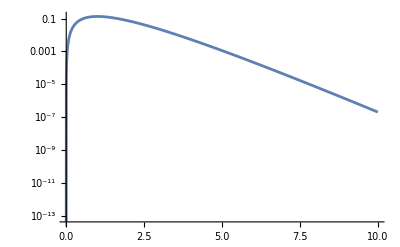

```mathematica
LogPlot[(ⅇ^(-2 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 k β)/(γ-k τ)^2/.{k->1,τ->1,γ->0.999,F0->1,k->1,β->1},{t,0,10}]
```

```mathematica
(ⅇ^(-4 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 β^2 (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(γ-k τ)^4/.{x->(ⅇ^(-(k t)/γ-t/τ) F0 (-ⅇ^((k t)/γ+t/τ) γ+ⅇ^(t/τ) γ-ⅇ^((k t)/γ) k τ+ⅇ^((k t)/γ+t/τ) k τ))/(k (-γ+k τ))}
```

```mathematica
(ⅇ^(-4 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 β^2 (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (γ-k τ) (F0-(ⅇ^(-(k t)/γ-t/τ) F0 (-ⅇ^((k t)/γ+t/τ) γ+ⅇ^(t/τ) γ-ⅇ^((k t)/γ) k τ+ⅇ^((k t)/γ+t/τ) k τ))/(-γ+k τ)))^2)/(γ-k τ)^4//FullSimplify
```

0

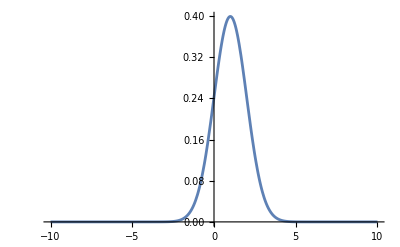

```mathematica
Plot[(ⅇ^(-(ⅇ^(-2 t (k/γ+1/τ)) β (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(2 k (γ-k τ)^2)) √(k β))/(√(2 π))/.{k->1,β->1,τ->1,F0->1,t->10,γ->0.999},{x,-10,10},PlotRange->All]
```

```mathematica
(ⅇ^(-4 t (k/γ+1/τ)) (ⅇ^((k t)/γ)-ⅇ^(t/τ))^2 F0^2 β^2 (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(γ-k τ)^4//TeXForm
```

\frac{\beta ^2 \text{F0}^2 e^{-4 t \left(\frac{k}{\gamma }+\frac{1}{\tau }\right)} \left(e^{\frac{k t}{\gamma
   }}-e^{t/\tau }\right)^2 \left(\text{F0} k \tau  e^{\frac{k t}{\gamma }}+(\text{F0}-k x) (\gamma -k \tau )
   e^{t \left(\frac{k}{\gamma }+\frac{1}{\tau }\right)}+\gamma  \text{F0} \left(-e^{t/\tau
   }\right)\right)^2}{(\gamma -k \tau )^4}

```mathematica
Integrate[(ⅇ^(-(a*x^2 + b*x +c)) √(k β))/(√(2 π))*x,{x,-Infinity,Infinity}]
```

ConditionalExpression[-(b ⅇ^(b^2/(4 a)-c) √(k β))/(2 √2 a^(3/2)), Re[a]>0]

```mathematica
Collect[-(ⅇ^(-2 t (k/γ+1/τ)) β (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (F0-k x) (γ-k τ))^2)/(2 k (γ-k τ)^2),x]
```

-1/2 k x^2 β-1/(2 k (γ-k τ)^2)ⅇ^(-2 t (k/γ+1/τ)) β (ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2)-(ⅇ^(-2 t (k/γ+1/τ)) x β (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2))/(2 k (γ-k τ)^2)

```mathematica
-(b ⅇ^(b^2/(4 a)-c) √(k β))/(2 √2 a^(3/2))/.{a->(1/2)*k*β,b->(ⅇ^(-2 t (k/γ+1/τ)) β (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2))/(2 k (γ-k τ)^2),c->1/(2 k (γ-k τ)^2)ⅇ^(-2 t (k/γ+1/τ)) β (ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2)}
```

```mathematica
-1/(2 k^2 (γ-k τ)^2)ⅇ^(-2 t (k/γ+1/τ)-(ⅇ^(-2 t (k/γ+1/τ)) β (ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2))/(2 k (γ-k τ)^2)+(ⅇ^(-4 t (k/γ+1/τ)) β (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2)^2)/(8 k^3 (γ-k τ)^4)) (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2)//FullSimplify
```

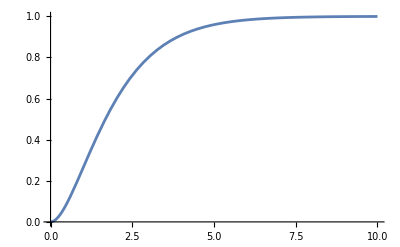

```mathematica
Plot[(F0 (γ-ⅇ^(-(k t)/γ) γ+(-1+ⅇ^(-t/τ)) k τ))/(k (γ-k τ))/.{F0->1,γ->0.999,τ->1,k->1},{t,0,10}]
```

```mathematica
D[(F0 (γ-ⅇ^(-(k t)/γ) γ+(-1+ⅇ^(-t/τ)) k τ))/(k (γ-k τ)),t]
```

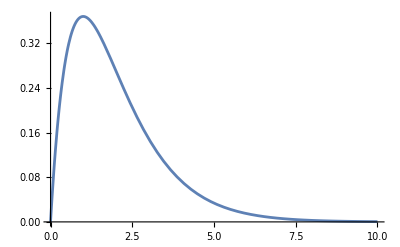

```mathematica
Plot[(F0 (ⅇ^(-(k t)/γ) k-ⅇ^(-t/τ) k))/(k (γ-k τ))/.{F0->1,k->1,τ->1,γ->0.999},{t,0,10}]
```